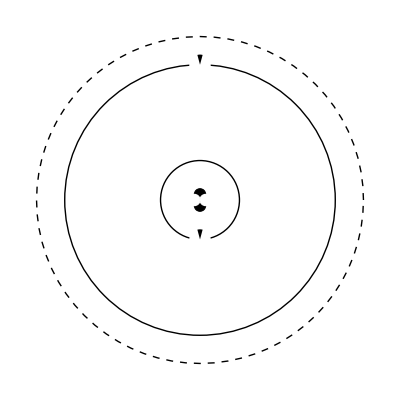

```mathematica
NuclearRadius = 4;
E1Radius = 3;
E2Radius = 20;
Show[{
Graphics[{Dashed,Circle[{0,0},25+NuclearRadius]}],
Graphics[Circle[{0,0},E2Radius+NuclearRadius]],
Graphics[{White,EdgeForm[Thick],Disk[{0,E2Radius+NuclearRadius},1.8]}],
Graphics[Circle[{0,0},E1Radius+NuclearRadius]],
Graphics[{Black,Disk[{0,E2Radius+NuclearRadius},1.8,{5Pi/12,7Pi/12}]}],
Graphics[{White,EdgeForm[Thick],Disk[{0,-(E1Radius+NuclearRadius)},1.8]}],
Graphics[{Black,Disk[{0,-(E1Radius+NuclearRadius)},1.8,{5Pi/12,7Pi/12}]}],
Graphics[{Black,EdgeForm[Thick],Disk[{0,1},1]}],
Graphics[{Black,EdgeForm[Thick],Disk[{0,-1},1]}],
Graphics[{White,EdgeForm[Thick],Disk[{1,0},1]}],
Graphics[{White,EdgeForm[Thick],Disk[{-1,0},1]}]
}]
```

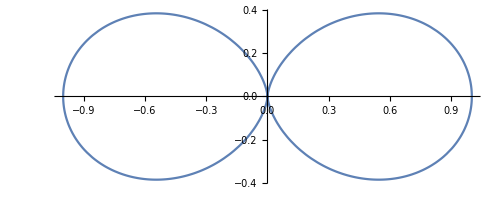

```mathematica
PolarPlot[Cos[θ]^2,{θ,0,2π}]
```

```mathematica
eV[l_]:=(6.63*10^-34*3*10^8)/(l*10^-9)1/(1.6*10^-19);
```

```mathematica
energies =25-{25,25-19.8,25-19.8-eV[1083],25-19.8-eV[403],25-19.8-eV[407],25-19.8-eV[412],25-19.8-eV[427]}
```

{0,19.8,20.9479,22.8847,22.8544,22.8173,22.7113}

```mathematica
(6.63*10^-34*3*10^8)/(1083*10^-9)1/(1.6*10^-19)
```

1.14785

```mathematica
(6.63*10^-34*3*10^8)/(407.7*10^-9)1/(1.6*10^-19)
```

3.04912

```mathematica
(6.63*10^-34*3*10^8)/(427.7*10^-9)1/(1.6*10^-19)
```

2.90653

```mathematica
(6.63*10^-34*3*10^8)/(402.7*10^-9)1/(1.6*10^-19)
```

3.07933

```mathematica
(6.63*10^-34*3*10^8)/(412*10^-9)1/(1.6*10^-19)
```

3.01729

```mathematica
{(NuclearRadius+P2Radius){Cos[π/2],Sin[π/2]},(NuclearRadius+P2Radius+eV[410]){Cos[π/2],Sin[π/2]}}
```

{{0.,31.725},{0.,34.757}}

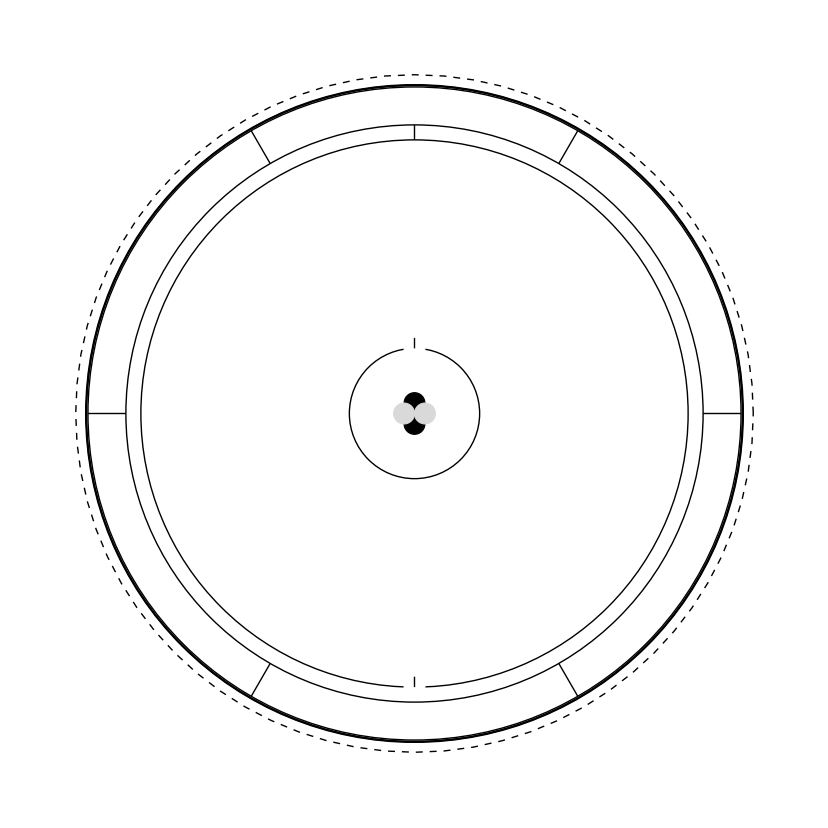

```mathematica
scale=1.5;
NuclearRadius = 1*scale;
IonRadius = 25 scale;
E1Radius = 4*scale+NuclearRadius;
E2Radius = 20scale+NuclearRadius;
P2Radius = E2Radius+1.15scale;
D5Radius = P2Radius+3.05scale;
ForbidRadius = P2Radius+2.9scale;
ESize = 1.2;
NSize = 1.2;
LineSet[n_,s_,λ_]:=Table[Graphics[{Line[{(P2Radius){Cos[2 k π/n+ s π/2],Sin[2k π/n+s π/2]},(P2Radius+scale eV[λ]){Cos[2k π/n+s π/2],Sin[2k π/n+s π/2]}}]}],{k,0,n-1}];
CircleSet[l_] := Map[Function[x,Graphics[Circle[{0,0},x]]],l];
Show[{
Graphics[{Dashed,Circle[{0,0},IonRadius+NuclearRadius]}],
Graphics[Circle[{0,0},E2Radius]],
Graphics[{White,EdgeForm[Thick],Disk[{0,-(E2Radius)},ESize]}],
Graphics[{Black,Line[{{0,(-E2Radius)},{0,-E2Radius+ESize}}]}],
Graphics[Circle[{0,0},E1Radius]],
Graphics[{White,EdgeForm[Thick],Disk[{0,(E1Radius)},ESize]}],
Graphics[{Black,Line[{{0,(E1Radius)},{0,(E1Radius)+ESize}}]}],
Graphics[{Black,EdgeForm[Thick],Disk[{0,NSize},NSize]}],
Graphics[{Black,EdgeForm[Thick],Disk[{0,-NSize},NSize]}],
Graphics[{LightGray,EdgeForm[Thick],Disk[{NSize,0},NSize]}],
Graphics[{LightGray,EdgeForm[Thick],Disk[{-NSize,0},NSize]}],
Graphics[{Black,Circle[{0,0},P2Radius]}],
CircleSet[P2Radius+scale*Map[eV[#1]&,{403,408,412,427}]],
LineSet[6,0,427],Graphics[{Line[{{0,E2Radius},{0,P2Radius}}]}]
}]
```

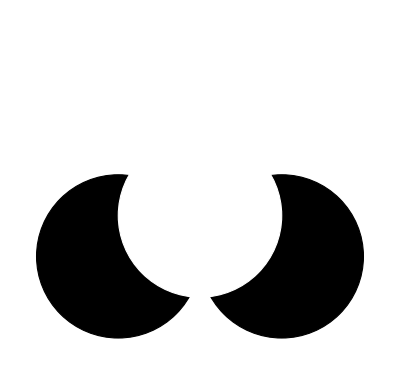

```mathematica
Show[{
Graphics[{White,EdgeForm[Thick],Disk[{0,√(3/2)},1]}],
Graphics[{Black,EdgeForm[Thick],Disk[{-1,-1/2},1]}],
Graphics[{Black,EdgeForm[Thick],Disk[{1,-1/2},1]}],
Graphics[{White,EdgeForm[Thick],Disk[{0,0},1]}]
}]
```

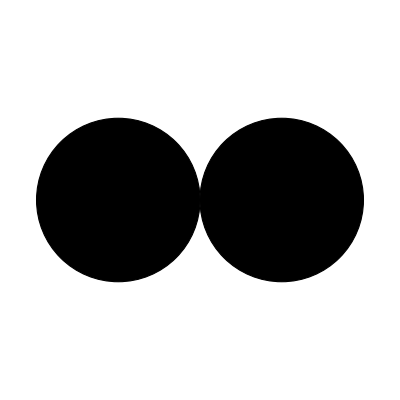

```mathematica
Show[{
Graphics[{White,EdgeForm[Thick],Disk[{0,1},1]}],
Graphics[{White,EdgeForm[Thick],Disk[{0,-1},1]}],
Graphics[{Black,EdgeForm[Thick],Disk[{1,0},1]}],
Graphics[{Black,EdgeForm[Thick],Disk[{-1,0},1]}]
}]
```